## Lesson

Identify languages:

```mathematica
LanguageIdentify[{"thank you","merci","dar las gracias","感謝","благодарить"}]
```

{English,French,Spanish,Chinese macrolanguage,Russian}

Identify images:

```mathematica
ImageIdentify[-Graphics-]
```

cheetah

Identify text sentiment:

```mathematica
Classify["Sentiment","I'm so excited to be programming"]
```

Positive

Perform more general classification:

```mathematica
Classify[{-Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 1},
 -Graphics-]
```

0

Find n nearest elements in a list:

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22]
```

{20}

```mathematica
Nearest[{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]},RGBColor[0.8727094319714808, 0.9066617343162084, 0.09569669807641734],3]
```

{Hue[0.15000000000000002],Hue[0.2],Hue[0.25]}

```mathematica
Nearest[WordList[],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

Perform OCR:

```mathematica
TextRecognize[-Graphics-]
```

hello

Find clusters:

```mathematica
FindClusters[RandomColor[50]]
```

{{RGBColor[0.15844818629206037, 0.8546437777255558, 0.41042200754516034],RGBColor[0.90821343418574, 0.7911473624681136, 0.8357093550286068],RGBColor[0.6604942574557453, 0.5496928170276274, 0.6714221141816965],RGBColor[0.8660688651542183, 0.6555223151180123, 0.507916567203136],RGBColor[0.8380659332480453, 0.8547220072568373, 0.2734073824111869],RGBColor[0.9751059296976472, 0.02110668056696796, 0.12453368118757235],RGBColor[0.4196520225831424, 0.572683505928109, 0.777165995716036],RGBColor[0.9955814692986125, 0.9324519432947205, 0.30112764238466894],RGBColor[0.32256250603936865, 0.4150804807588524, 0.478583015196147],RGBColor[0.3379482019832607, 0.7180487189967926, 0.8362662967376615],RGBColor[0.9245979344087178, 0.8789133687474535, 0.39886752963137484],RGBColor[0.7938610134594515, 0.7283230168557606, 0.7997674150949545],RGBColor[0.1440372445856457, 0.6379081933431592, 0.9963776493125704],RGBColor[0.7743246483740054, 0.4317367138435493, 0.37558323727822995],RGBColor[0.21515635533380584, 0.47164434561605484, 0.29770055429751396],RGBColor[0.36699577709540865, 0.6055880827976894, 0.7580584826095915],RGBColor[0.3370277823736896, 0.8848479591676925, 0.3868501467354528],RGBColor[0.602967322610195, 0.8210281253295639, 0.06980399419668526],RGBColor[0.43897233662354274, 0.5230887597775102, 0.21786446906398704],RGBColor[0.930507304587221, 0.6645511631737595, 0.33650339204293767],RGBColor[0.7469917947991291, 0.8932773171283801, 0.6486248210708943],RGBColor[0.353822270345701, 0.8062272120097747, 0.49558288874001377],RGBColor[0.5560779620838938, 0.011906680315331597, 0.36680743498623336],RGBColor[0.0477687442753465, 0.3652098018320682, 0.0824510777817018],RGBColor[0.11051965851192214, 0.2735379437003762, 0.5272992979755857],RGBColor[0.4998720552638338, 0.7247976245823491, 0.9335354333184236],RGBColor[0.6747093380958396, 0.6685169935999828, 0.05031977869906901],RGBColor[0.2855808407907192, 0.5167582113605957, 0.10159317999555029],RGBColor[0.8239580085000262, 0.5125308613641377, 0.594828127985827],RGBColor[0.21495988475097172, 0.28786406329837466, 0.4133914366818314],RGBColor[0.07907155739642113, 0.9168934028045166, 0.5707471827288215],RGBColor[0.7827819819720532, 0.4816216131129831, 0.4557478591590911],RGBColor[0.20360329582417358, 0.3434893489164088, 0.6320114083483861],RGBColor[0.27736745294352705, 0.5355582996759118, 0.4573758056480468],RGBColor[0.9588550990752425, 0.8158346614267944, 0.4374034759378884],RGBColor[0.5988468469808197, 0.7768822913567444, 0.20309881741124824],RGBColor[0.20572221794432632, 0.711110400629934, 0.40096717460041376],RGBColor[0.21175310793531765, 0.16010685968261407, 0.2458542331639859],RGBColor[0.8990117609985606, 0.4481544651091016, 0.6579712883698807],RGBColor[0.744035948653821, 0.6619783516084257, 0.4953732327214666],RGBColor[0.6181366182237544, 0.9817949570404716, 0.9712200500933623]},{RGBColor[0.7978080069286757, 0.370580635943889, 0.8346371584379146],RGBColor[0.6537359982946507, 0.4620626227819884, 0.9258333228459128],RGBColor[0.9360584519519883, 0.18160925576648257, 0.6814527179261987],RGBColor[0.8178937764570602, 0.13189149393484434, 0.8782200588110431]},{RGBColor[0.4418013701690935, 0.24732301752656527, 0.9606938833338909],RGBColor[0.3367372165523739, 0.08694676361624398, 0.8682257388481043],RGBColor[0.07583818616865323, 0.08484157459618569, 0.7767700192878526],RGBColor[0.12385540734272871, 0.19814290518920052, 0.9146417715636024],RGBColor[0.4009175845535591, 0.2676937411916174, 0.9380392851844459]}}

Plot clusters as graph:

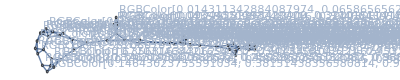

```mathematica
NearestNeighborGraph[RandomColor[50],3,VertexLabels->All]
```

Plot clusters as dendrogram:

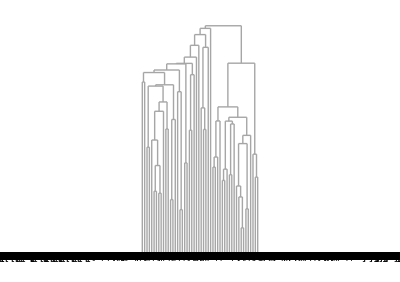

```mathematica
Dendrogram[RandomColor[50]]
```

Plot data based on features:

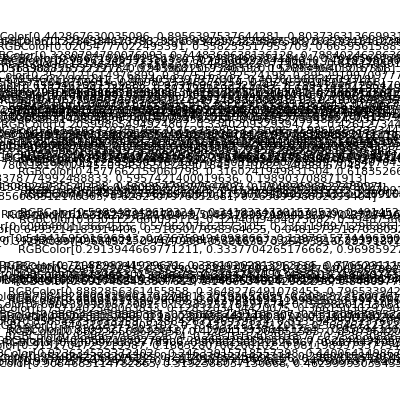

```mathematica
FeatureSpacePlot[RandomColor[100]]
```

## Questions

Q1. Identify what language the word “ajatella” comes from.

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

Q2. Apply ImageIdentify to an image of a tiger.

```mathematica
ImageIdentify[-Graphics-]
```

tiger

Q3. Make a table of image identifications for an image of a tiger, blurred by an amount from 1 to 5.

```mathematica
ImageIdentify[Blur[-Graphics-,#]]&/@Range[5]
```

{tiger,tiger,tiger,spiny-finned fish,fish}

Q4. Classify the sentiment of “I’m so happy to be here”.

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

Q5. Find the 10 words in WordList[ ] that are nearest to “happy”.

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

Q6. Generate 20 random numbers up to 1000 and find which 3 are nearest to 100.

```mathematica
Nearest[RandomInteger[1000,20],100,3]
```

{75,52,163}

Q7. Generate a list of 10 random colours, and find which 5 are closest to Red.

```mathematica
Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.714830579344458, 0.10829271021663955, 0.3768792964765242],RGBColor[0.6499888213875094, 0.26859291035880895, 0.3422051500452008],RGBColor[0.8686608993324345, 0.6527046268137449, 0.4714047456835899],RGBColor[0.6738824698035204, 0.5525136711481746, 0.4700511004697179],RGBColor[0.8334245489335232, 0.6215269676725117, 0.6629461066443911]}

Q8. Of the first 100 squares, find the one nearest to 2000.

```mathematica
Nearest[Range[100]^2,2000]
```

{2025}

Q9. Find the 3 European flags nearest to the flag of Brazil.

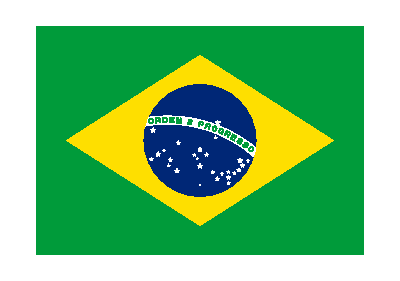
```mathematica
Nearest[#["Flag"]&/@Entity["GeographicRegion","Europe"]["Countries"],-Graphics-,3]
```

{-Graphics-,-Graphics-,-Graphics-}

Q10. Make a graph of the 2 nearest neighbours of each colour in Table[Hue[h], {h, 0, 1, .05}].

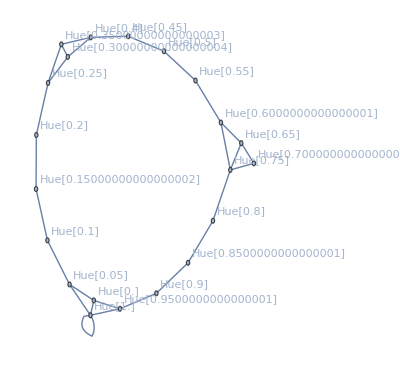

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,.05}],2,VertexLabels->Automatic]
```

Q11. Generate a list of 100 random numbers from 0 to 100, and make a graph of the 2 nearest neighbors of each one.

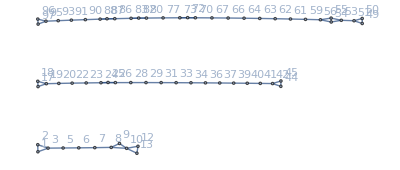

```mathematica
NearestNeighborGraph[RandomInteger[100,100],2,VertexLabels->Automatic]
```

Q12. Collect the flags of Asia into clusters of similar flags.

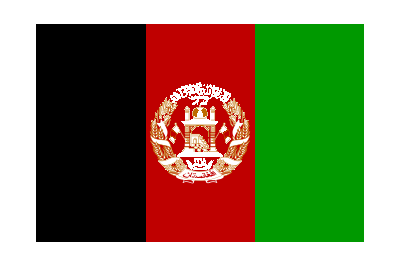
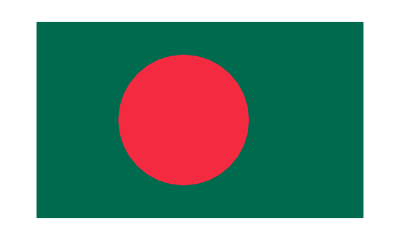
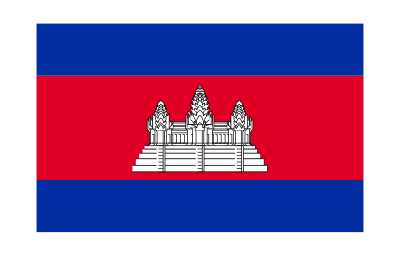
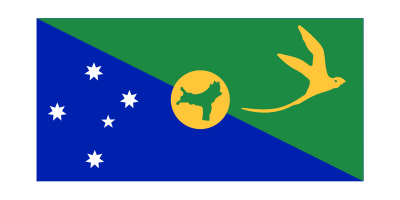
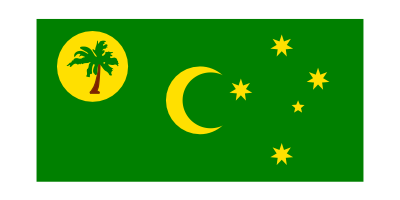
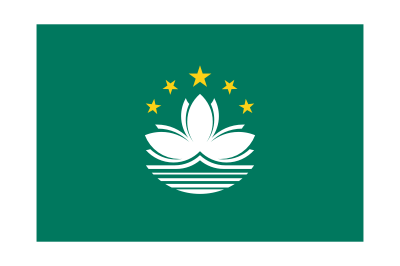
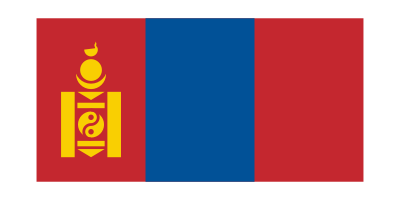
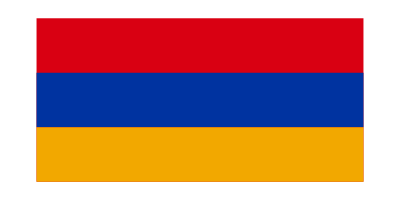

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[#["Flag"]&/@Entity["GeographicRegion","Asia"]["Countries"]]
```

Q13. Make raster images of the letters of the alphabet at size 20, then make a graph of the 2 nearest neighbors of each one.

```mathematica
NearestNeighborGraph[Rasterize[Style[#,20]]&/@Alphabet[],2,VertexLabels->Automatic]
```

-Graphics-

Q14. Generate a table of the results of using TextRecognize on “hello” rasterized at size 50 and then blurred by between 1 and 10.

```mathematica
TextRecognize[Blur[Rasterize[Style["hello",30]],#]&/@Range[10]]
```

{hello,hello,hello,hello,hello,hello,hello,hello,helle,nelle}

Q15. Make a dendrogram for images of the first 10 letters of the alphabet.

```mathematica
Dendrogram[Rasterize[#]&/@Alphabet[][[;;10]]]
```

-Graphics-

Q16. Make a feature space plot for the uppercase letters of the alphabet.

```mathematica
FeatureSpacePlot[Rasterize[#]&/@ToUpperCase[Alphabet[]]]
```

-Graphics-

## Extended Questions

+Q1. Make a table of image identifications for a picture of the Eiffel Tower, blurred by an amount from 1 to 5.

```mathematica
ImageIdentify[Blur[-Graphics-,#]&/@Range[5]]
```

{Eiffel Tower,Eiffel Tower,tower,stupa,stupa}

+Q2. Classify the sentiment of the Wikipedia article on “happiness”.

```mathematica
Classify["Sentiment",WikipediaData["happiness"]]
```

Neutral

+Q3. Of colours in the list Table[Hue[h], {h, 0, 1, .05}], find which are the 3 nearest to Pink.

```mathematica
Nearest[Table[Hue[h],{h,0,1,.05}],Pink,3]
```

{Hue[0.9500000000000001],Hue[0.9],Hue[0.05]}

+Q4. Compute all fractions i/j for i and j up to 500, and find the 10 fractions closest to pi.

```mathematica
Nearest[Flatten[Table[i/j,{i,500},{j,500}]],π,10]
```

{355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155}

+Q5. Generate a list of 10 random numbers from 0 to 10, and make a graph of the 3 nearest neighbors of each one.

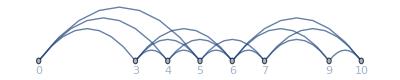

```mathematica
NearestNeighborGraph[RandomInteger[10,10],3,VertexLabels->Automatic]
```

+Q6. Find clusters of similar colours in a list of 100 random colours.

```mathematica
FindClusters[RandomColor[100]]
```

{{RGBColor[0.6191386858422918, 0.4177993789264043, 0.5270278288304122],RGBColor[0.9702624483081466, 0.2818945116084508, 0.6518142820665778],RGBColor[0.17924834887773144, 0.8847152520307704, 0.20100195881822747],RGBColor[0.2971356956587401, 0.7660328085359456, 0.4436639560300619],RGBColor[0.26935356886771644, 0.7095433530134911, 0.9743553871394277],RGBColor[0.5037448295587796, 0.41975236084862844, 0.9050789505166348],RGBColor[0.46128596880507433, 0.3059223235292414, 0.6835817210820068],RGBColor[0.9379601880422357, 0.4257944454925835, 0.9068621402560386],RGBColor[0.08355041335184565, 0.8859939686080147, 0.6676269350346653],RGBColor[0.3940679244556837, 0.826421019756971, 0.6544361077315142],RGBColor[0.6918369705074916, 0.9297496779869856, 0.9136683279122779],RGBColor[0.9406429851904383, 0.9606893778030134, 0.9199188366396023],RGBColor[0.8090202447665518, 0.4186021346962472, 0.7615262586306386],RGBColor[0.6886375900396879, 0.6485182422488227, 0.8350101982006963],RGBColor[0.08986141550966087, 0.8609085154788259, 0.2512910916395026],RGBColor[0.4883848525236745, 0.5812016969404197, 0.8520950908914562],RGBColor[0.9980358073954878, 0.05100888811645499, 0.6888529268074286],RGBColor[0.35458975616507793, 0.6306677539830263, 0.6787690890955023],RGBColor[0.31259356710678476, 0.7569749566879853, 0.2958740011653145],RGBColor[0.7781476620117334, 0.45840618383801934, 0.7844153018945996],RGBColor[0.25872823335263884, 0.6150513370805664, 0.6132148850875156],RGBColor[0.5089344051327833, 0.41273016297478016, 0.7213503855789203],RGBColor[0.9013999360409617, 0.602293827673928, 0.8120790684664401],RGBColor[0.6748052761003933, 0.01784121125010052, 0.5091675059184677],RGBColor[0.0305264991561065, 0.6364409360266161, 0.17956508207240707],RGBColor[0.4539913893262424, 0.8548085860039789, 0.007491123433375879],RGBColor[0.9190622115026139, 0.6815389862443129, 0.7382033725871384],RGBColor[0.6059196429758043, 0.36590427721641605, 0.840940556455587],RGBColor[0.5070918791433334, 0.24849079453053835, 0.5574386910122451],RGBColor[0.2697841233267093, 0.5231432942246728, 0.0270885883194254],RGBColor[0.5449147516836903, 0.970969620207246, 0.8485182330656758],RGBColor[0.46891479087143084, 0.8534835634699098, 0.23167397928610267],RGBColor[0.48489755402679746, 0.9118459398774594, 0.8398621141473703],RGBColor[0.13981049012556146, 0.8896383768483984, 0.5221464789112622],RGBColor[0.564939078017286, 0.7257550883874606, 0.9544103569150939],RGBColor[0.0007994637795596393, 0.7229049287176867, 0.8914301719247912],RGBColor[0.5688968131521919, 0.36615849769854036, 0.5828528028212527],RGBColor[0.6108248803400678, 0.6750042812797299, 0.895837575736923],RGBColor[0.858997229519062, 0.7680973600917114, 0.8135889204668718],RGBColor[0.8472024680327748, 0.8568846808662351, 0.9622538541876442],RGBColor[0.3332173082671619, 0.8459996121575875, 0.9690561045933312],RGBColor[0.7129366971991822, 0.5807572839144752, 0.6206621117503079],RGBColor[0.5065165567524341, 0.08835894448663328, 0.5727934495798217],RGBColor[0.134000391177576, 0.9996228606954116, 0.34118721336977575],RGBColor[0.13289666969208724, 0.9629328890114135, 0.0789279470283466],RGBColor[0.03164168509624843, 0.7988625750314622, 0.6288329479855681],RGBColor[0.14722858274953632, 0.876312992383131, 0.5940694139022225],RGBColor[0.8322328505217298, 0.28838526256058894, 0.6629334902468416],RGBColor[0.324080884229103, 0.5162864522553139, 0.774382525031827],RGBColor[0.04097378771760485, 0.5862976368679005, 0.7580975912467007]},{RGBColor[0.2767128796515377, 0.41576359687749354, 0.1799447930437339],RGBColor[0.27657798789057586, 0.554607472503218, 0.30692898999507423],RGBColor[0.14550343800573717, 0.5323350621444005, 0.39124295245432483],RGBColor[0.2807450304978556, 0.2882137124124171, 0.14018352287220437],RGBColor[0.10741503858293844, 0.4569423921791067, 0.20347388364538244]},{RGBColor[0.8943744348731657, 0.30780999897533645, 0.08329902955512414],RGBColor[0.8469544292937619, 0.3035271170999261, 0.30211833293290535],RGBColor[0.6391758532696221, 0.08486639405404217, 0.14435825941867408],RGBColor[0.8307904977649148, 0.35727944754831364, 0.3654802268119077],RGBColor[0.8725469175793588, 0.011675518568801113, 0.24996848971336405],RGBColor[0.9519013129258107, 0.45341671909606407, 0.3946537598979265],RGBColor[0.8622722420128457, 0.18480364438651709, 0.3719165472858246],RGBColor[0.9240554712892279, 0.5191643044926462, 0.536077162233386],RGBColor[0.8442002112716114, 0.09215409083070214, 0.21109444966453061],RGBColor[0.9103147301770917, 0.383043872352854, 0.1578064151529457],RGBColor[0.9542593225393918, 0.5695486079923473, 0.5219876510884622],RGBColor[0.9065184908445525, 0.4080847960031153, 0.21322684191932484]},{RGBColor[0.31809334305413506, 0.3835816380360584, 0.6421158870260271],RGBColor[0.2134497291354578, 0.3491042361329193, 0.45969525600907346],RGBColor[0.24192577820454297, 0.32905996147924066, 0.33945525710495117],RGBColor[0.16030910403138487, 0.36703455579642696, 0.48841785293365314],RGBColor[0.17277643493541883, 0.1603934599353496, 0.39721343096644524],RGBColor[0.22072510829836367, 0.17933648992794504, 0.22094417954421974],RGBColor[0.34871305052120993, 0.4566473363474224, 0.755299931709376]},{RGBColor[0.9560011463190043, 0.9062108211433599, 0.5851634049575936],RGBColor[0.7041984581265965, 0.6432524058267006, 0.09470420507315591],RGBColor[0.6887127298801143, 0.7035735882383847, 0.38097840246672066],RGBColor[0.7794612494114985, 0.9195744920048814, 0.29759357078865767],RGBColor[0.9049590910620784, 0.7786645155448504, 0.0009730020154352648],RGBColor[0.7722188033658157, 0.8625050418610773, 0.21844873308276402],RGBColor[0.8086772818734773, 0.74467455006169, 0.20399095926467892],RGBColor[0.8869040579745133, 0.7843250930038348, 0.5073141468789804],RGBColor[0.8350159742401155, 0.934923281844237, 0.4785678782403271]},{RGBColor[0.24514277370976645, 0.18140079685217825, 0.7499597906463269],RGBColor[0.0041894414834766636, 0.2545078900361384, 0.6855407968569092],RGBColor[0.1992423708276836, 0.21875312017649495, 0.8308456829196975],RGBColor[0.452080824611266, 0.11979544145768717, 0.7855536319661742],RGBColor[0.4141673275323705, 0.16662338370753527, 0.8886443271852755],RGBColor[0.36099816617331504, 0.10264963785980474, 0.7328752008101871],RGBColor[0.36670041268553, 0.27023457366162784, 0.9156703179093895]},{RGBColor[0.5738958558920553, 0.47141205536798725, 0.3398156815751945],RGBColor[0.47180888925805986, 0.2927239534759878, 0.2883719345972351],RGBColor[0.6701337480997291, 0.43935129578325527, 0.2673731749890058],RGBColor[0.9852427022456469, 0.6229639461977967, 0.11147804441068976],RGBColor[0.6855642391751637, 0.5183859922771341, 0.2770571395861017],RGBColor[0.4118857477065738, 0.12434815597053217, 0.03139322679881973],RGBColor[0.7049643103113123, 0.5073796393043035, 0.16002211800454136]},{RGBColor[0.8609599487184358, 0.19347221141327742, 0.9521152033238927],RGBColor[0.8490168159714597, 0.174877622665927, 0.8488477145365811],RGBColor[0.7406618120867356, 0.11021194012022395, 0.963821269898876]}}

+Q7. Make a feature space plot for both upper and lowercase letters of the alphabet.

```mathematica
FeatureSpacePlot[Rasterize/@Join[Alphabet[],ToUpperCase[Alphabet[]]]]
```

-Graphics-